```mathematica
(* This notebook analyzes the dynamics of NNC and BBC estimates of the FNR of the PR monitor, as well as their errors (MSE, RMSE), depending on the amount of the data provided to both analyses for estimation. NCC gets atomic pipeline detector traces as data; BBC gets PR monitor traces as data. *)
```

```mathematica
NotebookEvaluate[NotebookOpen[StringJoin[NotebookDirectory[],"file-ops.nb"]]];
```

```mathematica
(*** NCC ESTIMATES ***)
Clear[predPrMonFNRTheor];

predPrMonFNRTheor[detFPR_, monWin_, pDetNCH0_:0(* for this context *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);
```

```mathematica
(*** ANALYSIS ***)
```

```mathematica
Clear[getPrFNRPointEstsWithMonH1ct, getPrFNRPointEstsWithDetH1ct,getPIFPRPointEstsWithDetH0ct, getPrFNRPointEstResidualsWithH1ct,getPrFnrMSQPairsWithBins];

(* provides a list of triples: (monH1InfoCt, our mon FNR est, data mon FNR est) *) 
getPrFNRPointEstsWithMonH1ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predPrMonFNRTheor[predFPRfromData[#, detFilenames], winSize], predFNRfromData[#, monFilenames, winSize,(*monnum*)PRmonID]}&/@ sampleAcrossAllStatelessSubsets[seshNums, sampleCtPerSubset]), "h1count",monFilenames, winSize,(*monnum*)PRmonID];

(* provides a list of triples: (monH1InfoCt, our mon FNR est, data mon FNR est) *) 
getPrFNRPointEstsWithDetH1ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predPrMonFNRTheor[predFPRfromData[#, detFilenames], winSize], predFNRfromData[#, monFilenames, winSize,(*monnum*)PRmonID]}&/@ sampleAcrossAllStatelessSubsets[seshNums, sampleCtPerSubset]), "h1count",detFilenames, winSize, (*monnum*)PRmonID];

(* like above but testing function for detector *) 
getPIFPRPointEstsWithDetH0ct[ seshNums_, sampleCtPerSubset_]:= tallyInfoInTriplesets[({#,predFPRfromData[#, detFilenames]}&/@ sampleAcrossAllStatelessSubsets[seshNums, sampleCtPerSubset]), "h0count",detFilenames];

(* provides a list of absolute residuals for above: (h1InfoCt, abs residual for our mon FNR est, abs residual for data mon FNR est) *) 
getPrFNRPointEstResidualsWithH1ct[seshNums_, sampleCtPerSubset_, winSize_] := With[{gtValue=predPrMonFNRTheor[0.1, winSize]},({#[[1]], Abs[#[[2]]-gtValue],Abs[#[[3]]-gtValue]  } & /@ getPrFNRPointEstsWithMonH1ct[seshNums, sampleCtPerSubset, winSize])];

(* provides a list of (bin start, bin elem count, mean squared error for our appr, mean squared error for data appr) ; bin end determined by bin size *) 
getPrFnrMSQPairsWithBins[seshNums_, sampleCtPerSubset_, winSize_, binSize_]:= With[{h1CtTwoEstList= (*a list of triples (h1ct, our est, data est *) getPrFNRPointEstResidualsWithH1ct[seshNums, sampleCtPerSubset, winSize] },
(* convert h1cts into bin starts *) Flatten[#]&/@Transpose[{(Range[0,  Max@h1CtTwoEstList[[All,1]], binSize]),({Length@#, Mean@(#[[All,2]]^2), Mean@(#[[All,3]]^2)} &/@ binListsBy[h1CtTwoEstList, {First, 0, Max@h1CtTwoEstList[[All,1]]+binSize-1, binSize}])}]];
```

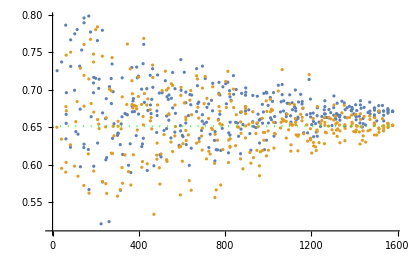
```mathematica
(*** POINT ESTIMATE PLOTS BY DATA AMOUNT ***) 

With[{data=getPrFNRPointEstsWithDetH1ct[{4,5,6,7}, 5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predPrMonFNRTheor[0.1, 10], Max@data[[All,1]]]]]
-Graphics-
```

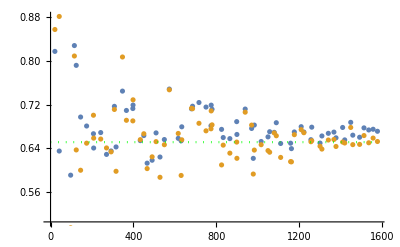

-Graphics-

```mathematica
With[{data=getPrFNRPointEstsWithMonH1ct[{4,5,6,7}, (*samples per subset size*)1, (*winsize*)10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predPrMonFNRTheor[0.1, (*winsize*)10], Max@data[[All,1]]]]]
```

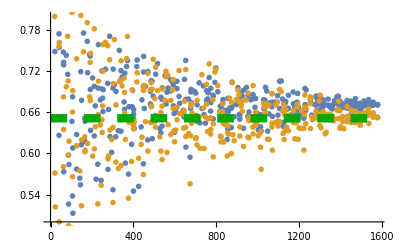

```mathematica
(* PRODUCTION-READY ESTIMATE PLOT (no CI line) *) 
plotPrFnr= With[{data=getPrFNRPointEstsWithMonH1ct[{4,5,6,7}, (*samples per subset size*)5, (*winsize*)10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]},PlotRange->{0.5,0.8}, PlotMarkers->{"OpenMarkers", Large}], chartHorLine[predPrMonFNRTheor[0.1, 10], Max@data[[All,1]],0, Darker@Green, {AbsoluteThickness[6],AbsoluteDashing[12]}]]]
```

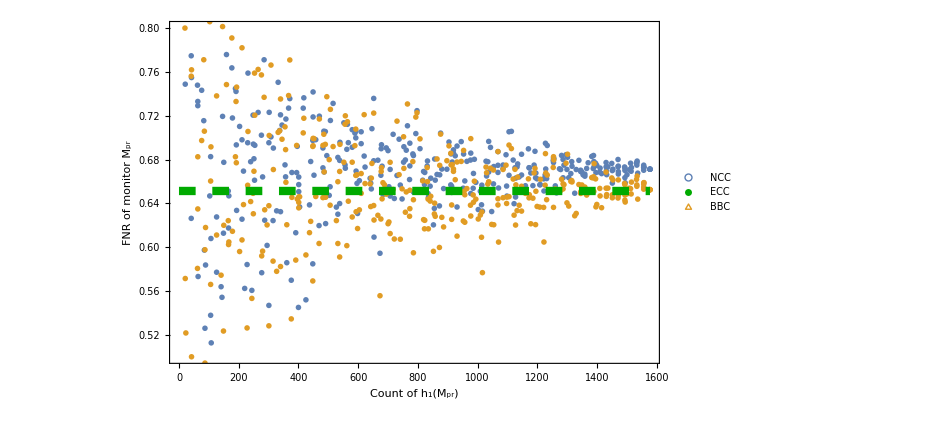

```mathematica
(* without CI line *) 
plotPrFnrLegended = Legended[Show[plotPrFnr, Frame->True, FrameLabel->{StringJoin["Count of ", ToString[ Style[StringJoin[ToString[Subscript[ "h", "1"],StandardForm], "(",ToString[Subscript[ "M", "pr"],StandardForm] ,")"], Italic], StandardForm] ],StringJoin["FNR of monitor ", ToString[Style[Subscript[ "M", "pr"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},{AbsoluteDashing[6],AbsoluteThickness[4],Darker@Green} , {ColorData[97,"ColorList"][[2]]}},{"NCC","ECC", "BBC"},
LegendMarkerSize->20,LegendMarkers->{Style[○,Bold,FontSize->28] , Graphics[{Line[{{-10,0},{10,0}}]}],Style[△,Bold,FontSize->28] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.9,0.2}]]
```

```mathematica
datafornow = getPrFNRPointEstsWithMonH1ct[{4,5,6,7}, (*samples per subset size*)5, (*winsize*)10];
```

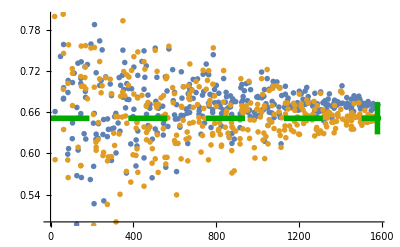

```mathematica
(* with CI line *) 
prfnrchart = With[{data=datafornow},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}, PlotRange->{0.5,0.8}, PlotMarkers->{Magnify[openMarkers[[1]], 4], Magnify[openMarkers[[2]],4]}], chartHorLine[predPrMonFNRTheor[0.1, (*winsize*)10], Max@data[[All,1]],0, Darker@Green, {Thickness[0.01](*AbsoluteThickness[6]*),AbsoluteDashing[28]}],ListPlot[{{Max@data[[All,1]],interWald[Max@data[[All,1]]*predPrMonFNRTheor[0.1, (*winsize*)10], Max@data[[All,1]], 0.95] }}, PlotStyle->{Darker@Green,Thickness[0.01]}]
]]
```

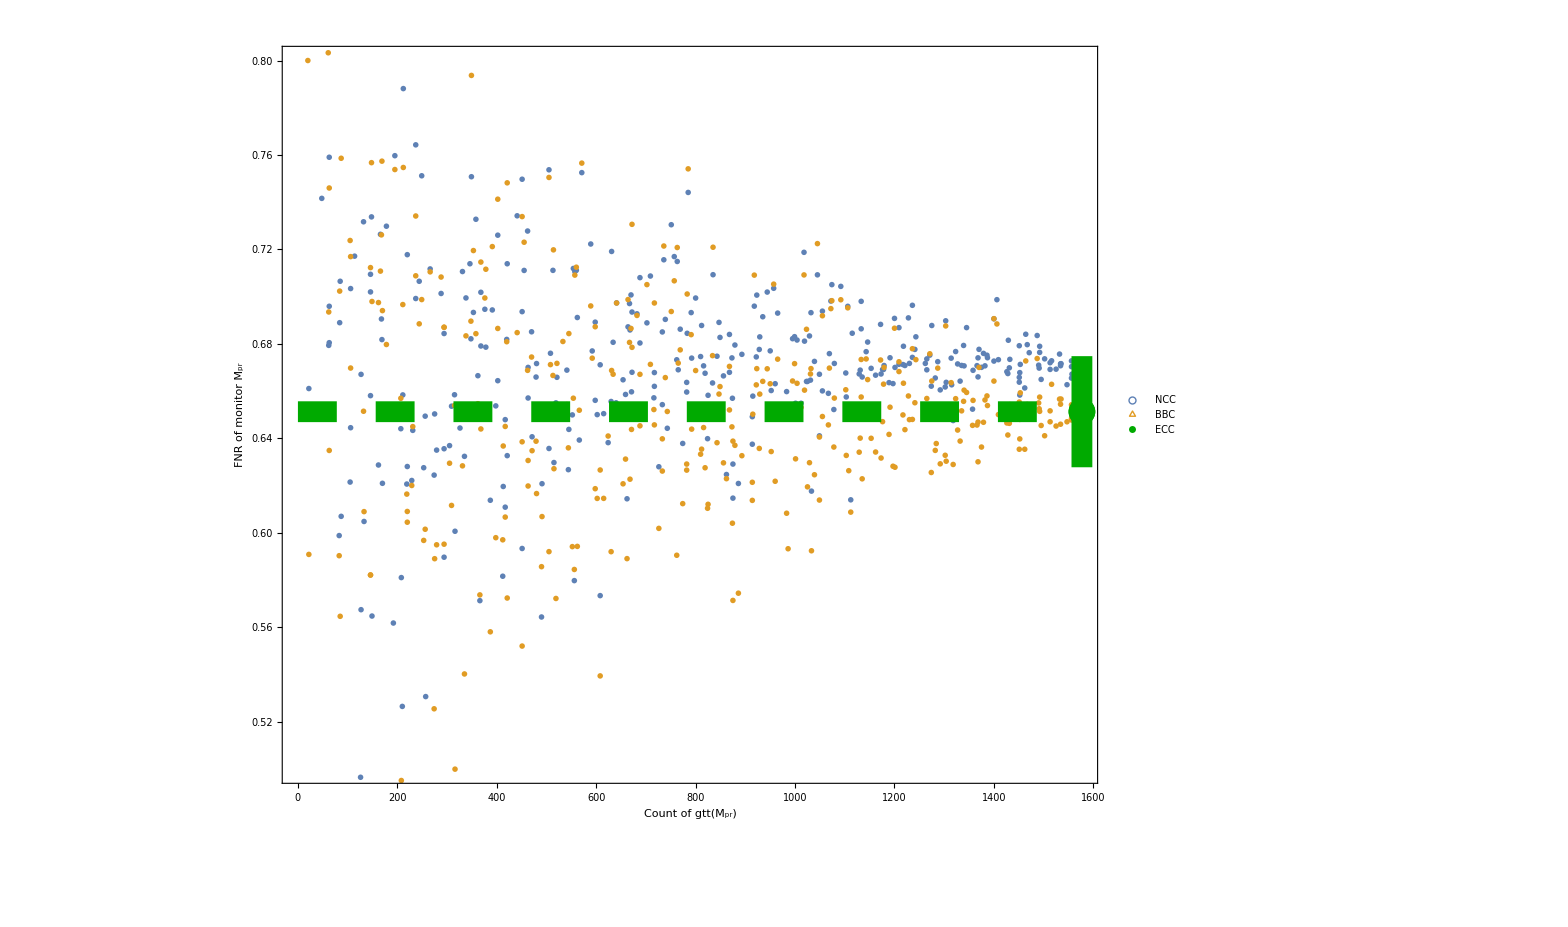

```mathematica
plotPrFnrLegended = Legended[Show[prfnrchart, Frame->True, FrameLabel->{StringJoin["Count of gtt", ToString[ Style[StringJoin[ "(",ToString[Subscript[ "M", "pr"],StandardForm] ,")"], Italic], StandardForm] ],StringJoin["FNR of monitor ", ToString[Style[Subscript[ "M", "pr"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->45}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},  {ColorData[97,"ColorList"][[2]]},{AbsoluteDashing[10],AbsoluteThickness[6],Darker@Green}},{"NCC","BBC","ECC" },
LegendMarkerSize->50,LegendMarkers->{Style[○,Bold,FontSize->55] ,Style[△,Bold,FontSize->60], Graphics[{Line[{{-10,0},{10,0}}]}](*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.9,0.2}]]
```

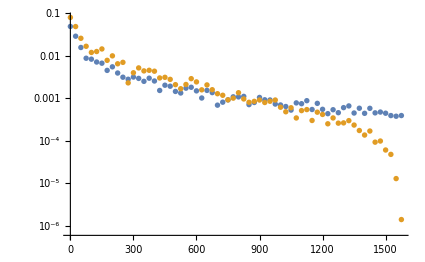

```mathematica
(** BINNED MSE PLOTS BY DATA QUANTITY **) 
Clear[data];(data = getFnrMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *)10, (* bin width *)25];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])
```

```mathematica
msePrdata={{0,37,0.04952981586725377,0.08066410723325736},{25,39,0.029192055257806528,0.04923302932802642},{50,41,0.015825218705444708,0.026062447255292685},{75,43,0.008832819468686953,0.016891660627116924},{100,42,0.008399909683368343,0.012102439861463532},{125,59,0.007194757024074231,0.012718573562340756},{150,46,0.006751683337828719,0.014612662044876663},{175,46,0.0045708414026471855,0.00788275461886156},{200,45,0.005545420378614478,0.010053420156386694},{225,41,0.003961111314793591,0.006539916472859259},{250,56,0.003157033046428468,0.007067036106172437},{275,42,0.0028244558262652416,0.002320369609163175},{300,44,0.0031858780132528216,0.004015302462463975},{325,50,0.0029590033044487613,0.005226112340331993},{350,42,0.0025241084333276743,0.004445580539431523},{375,49,0.0029913703836566973,0.004592340052171543},{400,45,0.002570723146370012,0.004373628905953624},{425,43,0.001538318071433719,0.0030315271195947226},{450,53,0.002045391966911909,0.0031364015302981015},{475,46,0.0019365376086748292,0.0028088446808885066},{500,42,0.0014592183512067587,0.002107653224709117},{525,51,0.001341371362625275,0.0016886837391206764},{550,43,0.0017430507669453496,0.0021258561333038603},{575,38,0.0018285657674336337,0.002917886615067157},{600,55,0.0015050629410553675,0.0024469924124533595},{625,40,0.0010215495415755345,0.0015916634544455674},{650,57,0.0015437167275312218,0.0020766204299089842},{675,46,0.0013697742156582957,0.0016017216011380271},{700,42,0.0006931744551154653,0.001289696741662015},{725,41,0.0008145325156051515,0.0011852080878589923},{750,48,0.0009248549451518371,0.000924954118537428},{775,51,0.0010893754938180122,0.001014851300808934},{800,47,0.001084668270504051,0.001361125104107679},{825,44,0.0011158267918015613,0.0009704172276652001},{850,44,0.0007135121759537312,0.0008097790199442174},{875,50,0.0008017829658734026,0.0008522204230405637},{900,48,0.0010533711284937523,0.0009159852139075933},{925,47,0.000927366489073891,0.000801434238001634},{950,42,0.0009178366221760056,0.0008566527579464198},{975,45,0.0007358751867999606,0.0009158588485302582},{1000,49,0.0007001600362691018,0.0006194518279350624},{1025,45,0.0006440439026313952,0.0004844283742524315},{1050,48,0.0005304015734245577,0.0006019785217215555},{1075,46,0.000783610735952896,0.000346119752374182},{1100,46,0.00075039155637751,0.000516030907094603},{1125,45,0.0008833946308614716,0.0005452496084047757},{1150,45,0.000547710420728247,0.00030210577652932673},{1175,47,0.0007638798363728501,0.000473455153798869},{1200,49,0.0005534783295272416,0.0004189942527016775},{1225,42,0.000436927498701829,0.00025232551043362226},{1250,45,0.0005410433718373611,0.0003464334902513444},{1275,46,0.00046102234631106924,0.00026126080721817596},{1300,52,0.0006060753983740977,0.00026498645701357535},{1325,50,0.0006646311170644211,0.00029951916278280686},{1350,39,0.00045250101819084625,0.00023553364603813597},{1375,43,0.0005867350132968008,0.0001752055555555938},{1400,48,0.00044511399720745075,0.00013711168512990074},{1425,44,0.0005837792177979779,0.00017039108257076217},{1450,60,0.0004564610659100412,0.00009320009649971713},{1475,42,0.00047706876757147256,0.00009906926432985413},{1500,40,0.0004476947933494785,0.00006085943910686495},{1525,41,0.00039420247530919317,0.00004799459708801235},{1550,38,0.00038014862820101624,0.000012920711210260915},{1575,40,0.000394508636146404,1.3999526929356987*^-6}};
```

```mathematica
(* from MSE to RMSE *)
rmsePrdata = msePrdata; rmsePrdata[[All,{3,4}]]  = Sqrt@rmsePrdata[[All,{3,4}]] ;
```

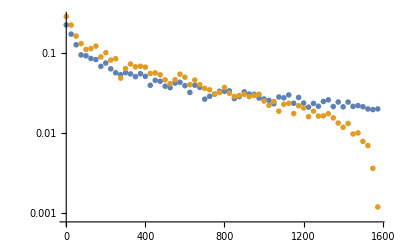

```mathematica
(* production-ready RMSE plot *) 
rmsePrplot = ListLogPlot[{rmsePrdata[[All,{1,3}]], rmsePrdata[[All,{1,4}]]}, PlotRange->All, PlotMarkers->{Magnify[openMarkers[[1]], 4], Magnify[openMarkers[[2]],4]}]
```

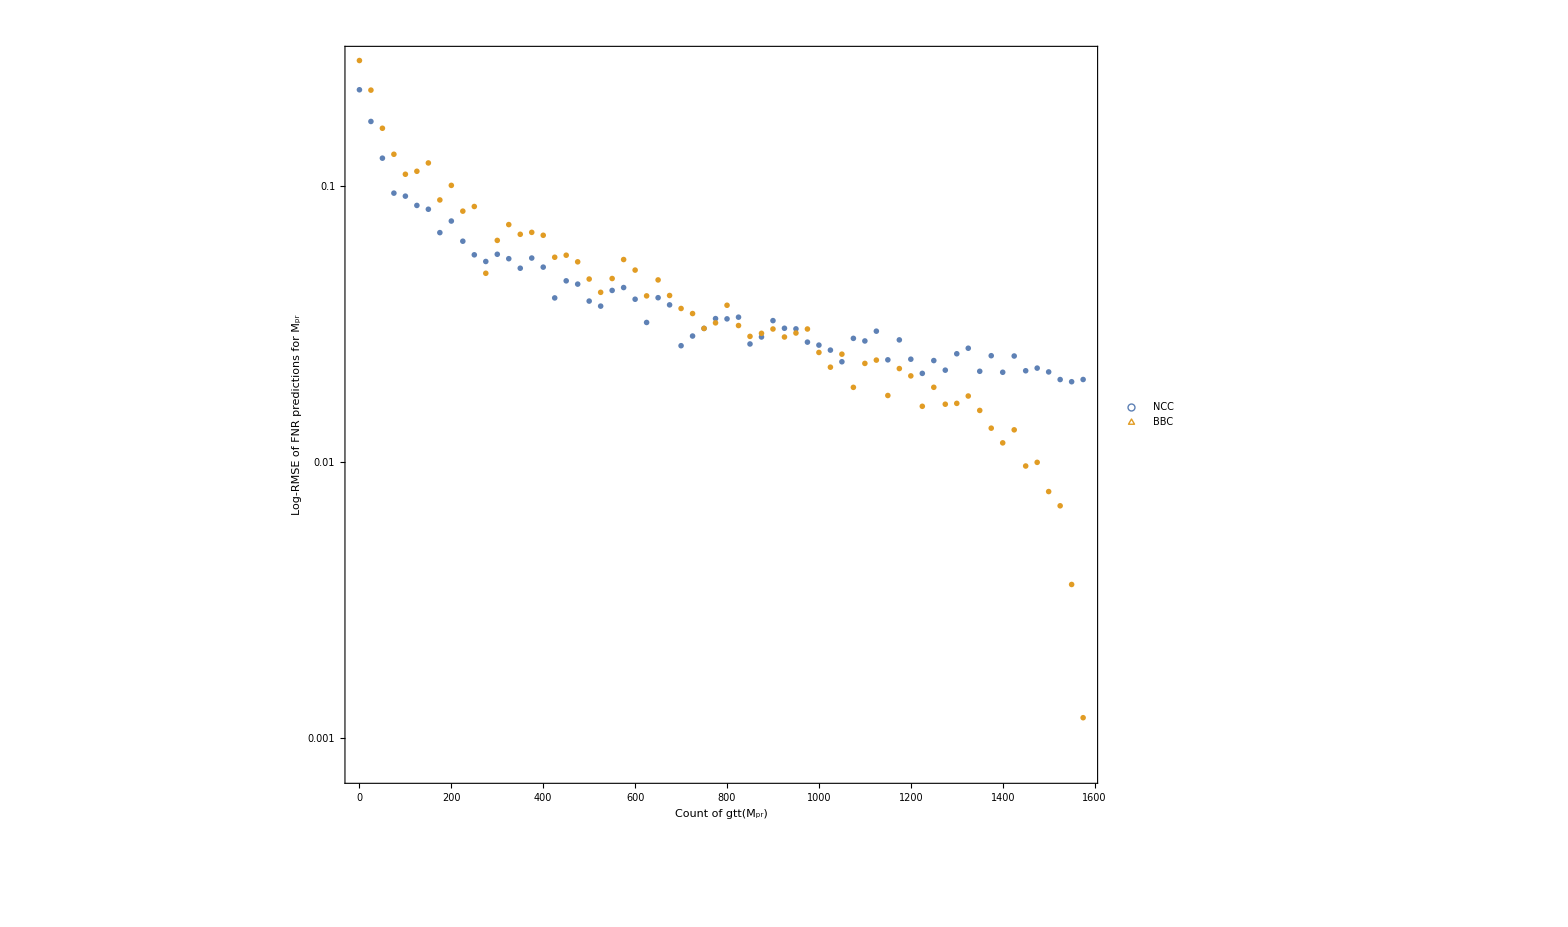

```mathematica
(* with a legend *) 
rmseRfplotLegended = Legended[Show[rmsePrplot, Frame->True, FrameLabel->{StringJoin["Count of gtt", ToString[ Style[StringJoin[ "(",ToString[Subscript[ "M", "pr"],StandardForm] ,")"], Italic], StandardForm] ], StringJoin["Log-RMSE of FNR predictions for ", ToString[Subscript[ "M", "pr"], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->45}],Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]} , {ColorData[97,"ColorList"][[2]]}},{"NCC", "BBC"},
LegendMarkerSize->50,LegendMarkers->{Style[○,Bold,FontSize->55] , Style[△,Bold,FontSize->60] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.1,0.2}]]
```